```mathematica
(* get the radius function right *)
```

## Styles and files

```mathematica
githubPath= PersistentSymbol["persistentGitHubPath","Local"];
AppendTo[$Path,FileNameJoin[{githubPath,"Packages"}]];
Needs["LatticePhyllotaxis`"];
Needs["DiskStacking`"];
Get["scpPaperStylings.m"]
```

```mathematica
gDrive = PersistentSymbol["persistentGDrive"];
runDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Runs"}];
eSetDirectory = (* post processed runs, no real reason for this to be different from runDirectory *) FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\Mathematica\\Esets"}];

draftFigureDirectory = FileNameJoin[{gDrive,"Work\\Textbook\\Stacked coin paper\\DraftFigures"}];



getRunByTag[tag_] := Module[{file},
file = FileNameJoin[{runDirectory,StringJoin[tag,".mx"]}];
If[FileExistsQ[file],Return[Import[file]]];
Print["Can't load ", tag, " from ", file];
Abort[]
];
```

```mathematica
jParastichyColour[n_] := jStyle["ParastichyColour"][n];
jFont[n_] := {FontFamily->  jStyle["FontFamily"],FontSize-> n};
paraColours= <|Red-> jParastichyColour[1],Blue-> jParastichyColour[2]|>;
leftRightColours = <|"Left"-> jParastichyColour[1],"Right"-> jParastichyColour[2]|>;
jBaseStyle= jFont[12];

SetAttributes[jExport,HoldFirst];

jExport[fig_] := Module[{figname},
SetDirectory[draftFigureDirectory];
figname=SymbolName[Unevaluated[fig]];
Export[StringJoin[figname,".jpg"],fig,ImageResolution->300];Export[StringJoin[figname,".pdf"],fig,ImageResolution->300];
ResetDirectory[];
(*fig
*)];
```

## 6 fig : scpConeTransformation runs but figure is wrong

### Get run

```mathematica
arena= <|"runNumber"->1
,"Tag"->"radius-34bis-recrease"
,"Run"->""
,"radiusFunctionParameters" -> {
<|"Type"->"LinearReduction","rScale"->40,"rSlope"->0.03|>
,<|"Type"->"Constant","ApproximateChains"->3|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"->1/5,"zRange"->2|>
}
,"Noise"->0
,"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{0,1}]
|>;
(*runCone  = doOneRun[arena];
*)
```

### Get run

```mathematica
arena2= <|"runNumber"->1
,"Tag"->"radius-34bis-crecrease"
,"Run"->""
,"radiusFunctionParameters" -> {
<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"->1.7,
"zRange"-> 0.1|>
,<|"Type"->"Constant","ApproximateChains"->1|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.9,"zRange"->0.02|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.4/0.9,"zRange"->0.15|>
,<|"Type"->"LinearCircumferenceIncrease","circumferenceScale"-> 0.2/(0.4/0.9),"zRange"->0.15|>
}
,"Noise"->0
,"Lattice"->LatticePhyllotaxis`latticeOrthogonal[{21,34},cylinderLU={-0.01,0.1}]
|>;
(*
runCone2  = doOneRun[arena2];

*)
```

```mathematica
runCone= getRunByTag["radius-34bis-crecrease"]["Run"];
stemParameters = runCone["Arena"]["rFunctionList"] ;
stemParameters = KeyMap[<|1->"cone",2->"bract",3->"ray",4->"seed",5->"inner"|>[#]&,stemParameters];
```

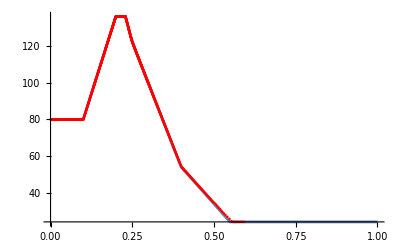

```mathematica
getf= retrieveRFunction[runCone] ; ht=runDisksHeight[runCone]; ra=runDisksRadius[runCone]; getr = Map[{ht[#],1/ra[#]}&,
Select[diskNumbersInRun[runCone],#>0&]];
Show[{Plot[1/getf[z],{z,0,1}],
ListPlot[getr,PlotStyle->Red]}]
```

## Disk map

```mathematica
makeDiskGraphics[run_] :=Module[{runDiskTransform,namedPolygons,namedType,namedPoints,colouredNodes,cropDisk,colouredPolygons,namedDiskNodes},
runDiskTransform := diskTransform[{stemParameters["ray"]["zStart"],stemParameters["inner"]["zEnd"]}];
namedDiskNodes = runTransformedNodes[run,runDiskTransform] ;
namedPolygons = namedPointsToVoronoiPolygons[namedDiskNodes];

namedPolygons = runTransformedToNamedPolygons[run,runDiskTransform];
namedType = nodeType /@  runTransformedNodes[run,Identity];
namedPoints = Point /@ runTransformedNodes[run,runDiskTransform];
colouredNodes= Association@Map[#->{nodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];
cropDisk = {FaceForm[White],EdgeForm[None],MeshPrimitives[DiscretizeRegion[RegionDifference[Rectangle[1.2*{-1,-1},1.2*{1,1}],Disk[]]],2]};colouredPolygons =Map[{baseColour[namedType[#]],EdgeForm[None],namedPolygons[#]}&,
Keys@namedPolygons];
diskShow  = Graphics[{
colouredPolygons
,cropDisk
,Values[colouredNodes]
},
PlotRange->{{-1.1,1.1},{-1.1,1.1}}
]
];



runTransformedNodes[run_,transform_,bareOnly_:False] := Module[{g,nodeNames,namedNodes,namedDiskNodes},
g=run["ContactGraph"];
If[bareOnly,
nodeNames = diskNumbersInRun[run],
nodeNames = VertexList[g]
];
(* not VertexList[g] unless we want left right, so this is only for disk at the moment  *)
namedNodes = Association@Map[#->AnnotationValue[{g,#},VertexCoordinates]&,nodeNames];
namedNodes= Select[namedNodes,#=!= $Failed&];
namedDiskNodes = transform /@ namedNodes;
namedDiskNodes
];

namedPointsToVoronoiPolygons[namedPoints_] := Module[{voronoi,vPolygons,polygonToPoint},
voronoi= VoronoiMesh[Values[namedPoints]];
vPolygons = MeshPrimitives[voronoi,2];
polygonToPoint[polygon_] := Module[{f,node},
f=RegionMember[polygon];
node= First@Keys@Select[namedPoints,f];
node -> polygon
];
Association@Map[polygonToPoint,Take[vPolygons,All]]
];
```

```mathematica
nodeType[{x_,z_}] := 
Which[
z<stemParameters["cone"]["zEnd"],"cone"
,z<stemParameters["bract"]["zEnd"], "bract"
,z<stemParameters["ray"]["zEnd"], "ray"
,z<stemParameters["seed"]["zEnd"],"seed"
,z<∞,"inner"
, True, Missing[]
];
```

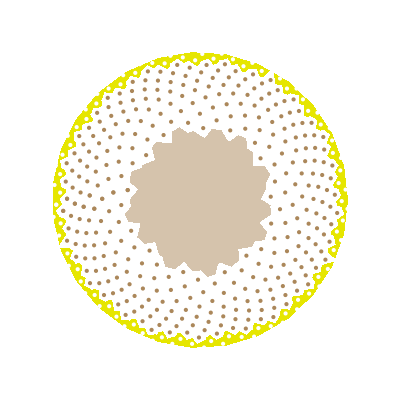

```mathematica
diskRun = DiskStacking`pruneRun[runCone,{stemParameters["ray"]["zStart"],stemParameters["inner"]["zEnd"]}];
diskShow :=makeDiskGraphics[diskRun]
diskShow
```

```mathematica
makeCylinderGraphics[run_] := Module[{},
namedPoints = Point /@ runTransformedNodes[run,Identity,bareOnly=True];
namedType = nodeType /@  runTransformedNodes[run,Identity];
colouredNodes= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];
namedDisks = runDisks[run];
colouredDisks= Association@Map[#->{cylinderNodeColour[namedType[#]],namedDisks[#]}&,Keys[namedDisks]];
partLabels =<|"cone"->"Uncommitted","bract"->"Bracts","ray"->"Ray florets","seed"-> "Seeds","inner"->"Unset seeds"|>;
partText =Style[KeyValueMap[Text[partLabels[#1],{0.55,Mean[{#2["zStart"],#2["zEnd"]}]},{-1,0}]&,stemParameters],jFont[12]];
cropRectangle = {FaceForm[White],EdgeForm[None],Rectangle[{1/2,-1},{2,10}]};
Graphics[{Values@colouredDisks,cropRectangle,partText},PlotRange->{{-1/2,1},Automatic}]
];
```

```mathematica
doDiskTransform[Disk[xz_,r_],transform_]:= Disk[transform[xz],r];
```

```mathematica
yellow3D=Darker[Yellow,0.1];
blackEdged[colour_] := Directive[EdgeForm[Black],FaceForm[colour],colour]

baseColour =  <|
"cone"-> LightGray,
"bract"-> jParastichyColour[3],
"ray"->Darker[Yellow,0.1],
"seed" -> White,
"inner"->Lighter[ColorData["CoffeeTones"][0.3],0.5]
|>;

nodeColour = baseColour;
nodeColour["ray"] = White;
nodeColour["seed"] = ColorData["CoffeeTones"][0.3];

cylinderNodeColour = baseColour;
cylinderNodeColour["seed"] = nodeColour["seed"];
```

```mathematica
stemParameters
```

<|cone→<|Type→LinearCircumferenceIncrease,circumferenceScale→1.7,zRange→0.1,rStart→0.0125117,rEnd→0.00735984,rScale→0.588235,zStart→0.0995617,zEnd→0.199562,rFunction→Function[{z$},0.00125117/(0.199562+1.7 (-0.0995617+z$)-z$)]|>,bract→<|Type→Constant,ApproximateChains→1,rStart→0.00735984,rEnd→0.00735984,zStart→0.199562,zEnd→0.229001,rFunction→Function[{z$},0.00735984]|>,ray→<|Type→LinearCircumferenceIncrease,circumferenceScale→0.9,zRange→0.02,rStart→0.00735984,rEnd→0.0081776,rScale→1.11111,zStart→0.229001,zEnd→0.249001,rFunction→Function[{z$},0.000147197/(0.249001+0.9 (-0.229001+z$)-z$)]|>,seed→<|Type→LinearCircumferenceIncrease,circumferenceScale→0.444444,zRange→0.15,rStart→0.0081776,rEnd→0.0183996,rScale→2.25,zStart→0.249001,zEnd→0.399001,rFunction→Function[{z$},0.00122664/(0.399001+0.444444 (-0.249001+z$)-z$)]|>,inner→<|Type→LinearCircumferenceIncrease,circumferenceScale→0.45,zRange→0.15,rStart→0.0183996,rEnd→0.040888,rScale→2.22222,zStart→0.399001,zEnd→0.549001,rFunction→Function[{z$},0.00275994/(0.549001+0.45 (-0.399001+z$)-z$)]|>|>

```mathematica
stemParameters["cone"]["zStart"]
```

0.0995617

```mathematica
cylinderRun = DiskStacking`pruneRun[stemParameters,{stemParameters["cone"]["zStart"],stemParameters["inner"]["zEnd"]}];cylinderShow = makeCylinderGraphics[cylinderRun];
cylinderShow
```

-Graphics-

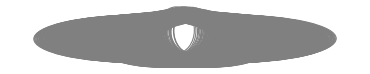

```mathematica
rCircumferenceTransform[r_] := 1/r;xzCircumferenceTransform[xz_,r_] := Module[{x,z},
{x,z}=xz;
x = x * rCircumferenceTransform[r];
{x,z}
];
xzCircumferenceTransform[Disk[xz_,r_]] := Ellipsoid[xzCircumferenceTransform[xz,r],
{rCircumferenceTransform[r],1}];
disks = runDisks[runCone,bareOnly=False];
Graphics[{ffs,Values@Map[xzCircumferenceTransform,disks]}]
```

```mathematica
run=runCone;transform := xzRadiusScalingTransform;
namedPoints = Point /@ runTransformedNodes[run,transform,bareOnly=True];
namedPoints
```

```mathematica
runTransformDisksByCircumference[run_] := Module[{g,disks},
disks =runDisks[run];

disks = Map[doDiskTransformRadius[#,transformRadius]& , disks];
disks
];
```

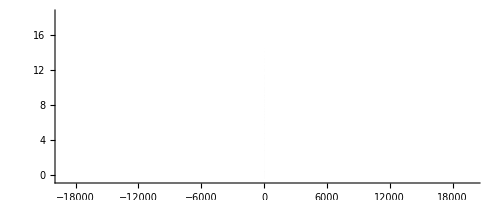

```mathematica
makeCone2DGraphics[run_] := Module[{},


transform := rScalingTransform;
namedPoints = Point /@ runTransformedNodes[run,transform,bareOnly=True];
namedType = nodeType /@  runTransformedNodes[run,transform];
colouredNodes= Association@Map[#->{cylinderNodeColour[namedType[#]],PointSize[Small],namedPoints[#]}&,Keys[namedPoints]];
namedDisks = runTransformedRadiusToDisks[run,transform];
colouredDisks= Association@Map[#->{cylinderNodeColour[namedType[#]],namedDisks[#]}&,Keys[namedDisks]];

Graphics[Values@colouredDisks,PlotRange->All]
];
cone2DShow = makeCone2DGraphics[runCone];
Show[cone2DShow,Axes->True]
```

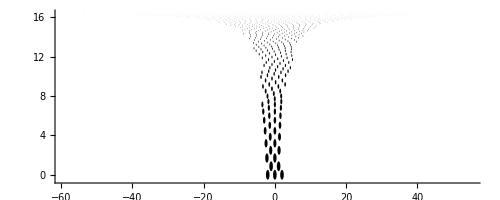

```mathematica
Graphics[{Take[Values[runTransformedToDisks[run,coneTransform2D[stemParameters]]],{1,1000}]},Axes->True]
```

```mathematica
diskTransform[{zMin_,zMax_}] := Module[{f},
f= Function[{xz},Module[{x,z,r},
{x,z}=xz;
r = zMax- z;
r= r/(zMax-zMin); (* outer ring radius 1 *)
r*{Cos[2 π x],Sin [ 2 π x]} 
]
];
f
];
coneTransform2DRadius :=  Module[{f},
f= Function[{xz},Module[{x,z,rScale},
{x,z}=xz;
rScale = 1/r;
x = x *r;
{x,z}
]
];
f
];
coneTransform2D[stemParameters_] := Module[{f},
f= Function[{xz},Module[{x,z,rScale},
{x,z}=xz;
rScale = stemParameters["cone"]["rFunction"][z];
x = x/rScale;
{x,z}
]
];
f
];
```

```mathematica
diskGraphics[run_,transform_] := Module[{g,g2,lp,nodes,zRange,vMesh,runDiskTransform,colouredNodes},
g=run["ContactGraph"];
nodes=AnnotationValue[g,VertexCoordinates];
diskNodes= transform /@  nodes;
(*vMesh= voronoiMeshNoEdge[nodes,{stemParameters["zUpperRim"],stemParameters["zCutoff"]}];
lp=meshToTransformedGraphics[vMesh,transform];
*)
colouredNodes= Map[{xStyle[nodeType[#]],PointSize[Medium],Point[transform[#]]}&,Select[nodes,!(MissingQ[nodeType[#]]
|| nodeType[#]=="Inner seeds") &]];

(*contactLines= Last/@Select[graphToContactLines[run],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&];
diskContactLines ={RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Map[meshToTransformedGraphics[#,transform]["Lines"]&,contactLines]};
*)
g2=Graphics[{
{EdgeForm[None],FaceForm[White],lp["Polygons"]}
,lp["Lines"],diskContactLines,{FaceForm[White],Disk[{0,0},0.4]},
colouredNodes},Method->{"ShrinkWrap" -> True}];
g2=Graphics[{
colouredNodes}];
g2
];
```

## Cruft

```mathematica
showDiskMeshFromNodes[g_] := Module[{gstyle,nodes,vx,mask},
nodes=AnnotationValue[g,VertexCoordinates];
v=VoronoiMesh[nodes];
v=Region[Style[v,EdgeForm[Black],FaceForm[None]]];
mask= DiscretizeRegion@RegionDifference[Rectangle[{-2,-2},{2,2}],Disk[]];
mask=Region[Style[mask,White]];
gstyle=Graph[g,VertexSize->Large,VertexStyle->Gray];
Show[gstyle,v,mask,PlotRange->{{-1,1},{-1,1}}]
];
```

```mathematica
stackGraphics[run_]:= Module[{disks,diskStyle,contactLines},
disks=Values[Map[#Disk&,run["DiskData"]]];
diskStyle[p:Disk[xz_,r_]] := {xStyle[nodeType[xz]],p};
contactLines= {RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Last/@Select[graphToContactLines[run,leftRightColours],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&]};
 Graphics[{ffs,diskStyle/@disks,{contactLines}},PlotRange->{{-1/2,1/2},{4.3,5.1}},PlotRangeClipping->True]
];
```

```mathematica
diskGraphics[run_,transform_] := Module[{g,g2,lp,nodes,zRange,vMesh,runDiskTransform,colouredNodes},
g=run["ContactGraph"];
nodes=AnnotationValue[g,VertexCoordinates];
vMesh= voronoiMeshNoEdge[nodes,{stemParameters["zUpperRim"],stemParameters["zCutoff"]}];
lp=meshToTransformedGraphics[vMesh,transform];

colouredNodes= Map[{xStyle[nodeType[#]],PointSize[Medium],Point[transform[#]]}&,Select[nodes,!(MissingQ[nodeType[#]]
|| nodeType[#]=="Inner seeds") &]];

contactLines= Last/@Select[graphToContactLines[run,leftRightColours],First[#]==RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226]&];
diskContactLines ={RGBColor[0.7194116276462343, 0.32145384723880266, 0.27090344303450226],Map[meshToTransformedGraphics[#,transform]["Lines"]&,contactLines]};

g2=Graphics[{
{EdgeForm[None],FaceForm[White],lp["Polygons"]}
,lp["Lines"],diskContactLines,{FaceForm[White],Disk[{0,0},0.4]},
colouredNodes},Method->{"ShrinkWrap" -> True}];
g2
];
```

```mathematica
polygonTransform[Polygon[poly___],transform_] := (Polygon[Map[transform,poly]]);
lineTransform[Line[line___],transform_] := (Line[Map[transform,line]]);
```

```mathematica
ffs= Directive[FaceForm[None],EdgeForm[Gray]];
```

```mathematica
meshToTransformedGraphics[vMesh_,transform_] := Module[{lMesh,lMesh2,lines2,lines3,rmesh,polys2,polys3},
lMesh = MeshRegion[MeshCoordinates[vMesh],MeshCells[vMesh,1]];
lMesh2= DiscretizeRegion[lMesh,MaxCellMeasure->{"Length"->.005}];
lines2= MeshPrimitives[lMesh2,1];
lines3= lineTransform[#,transform]&/@lines2;
rmesh =DiscretizeRegion[vMesh,MaxCellMeasure->{"Length"->.01}];polys2= MeshPrimitives[rmesh,2];
polys3= Map[polygonTransform[#,transform]&,polys2];
<|"Lines"->lines3,"Polygons"->polys3|>
];
```